```mathematica
Remove["CppClassLayoutParser`*"];
SetDirectory[NotebookDirectory[]];
<<"CppClassLayoutParser1.wl"
```

```mathematica
classes=ParseCppToClasses["previos_exam_examples/Q2_W23-24_A.hpp"];
```

```mathematica
layoutY1=ComputeClassLayout[classes,"Y1"]
```

<|ClassName→Y1,Layout→{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,Align→8,ClassOfVtable→Y1,VTableEntries→{Y1::f,Y1::g1}|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,Align→8,IsVirtualBase→True,VBaseOf→X|>,<|Name→Y1,Kind→Class,Offset→16,Size→0,Align→1|>},VirtualBases→{<|ClassName→X,Layout→{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,Align→8,ClassOfVtable→Y1,VTableEntries→{X::f,X::g2}|>,<|Name→X,Kind→Class,Offset→8,Size→4,Align→4|>},TotalSize→16,MaxAlign→8,VTableEntries→{X::f,X::g2}|>},TotalSize→16,MaxAlign→8,VTableEntries→{Y1::f,Y1::g1}|>

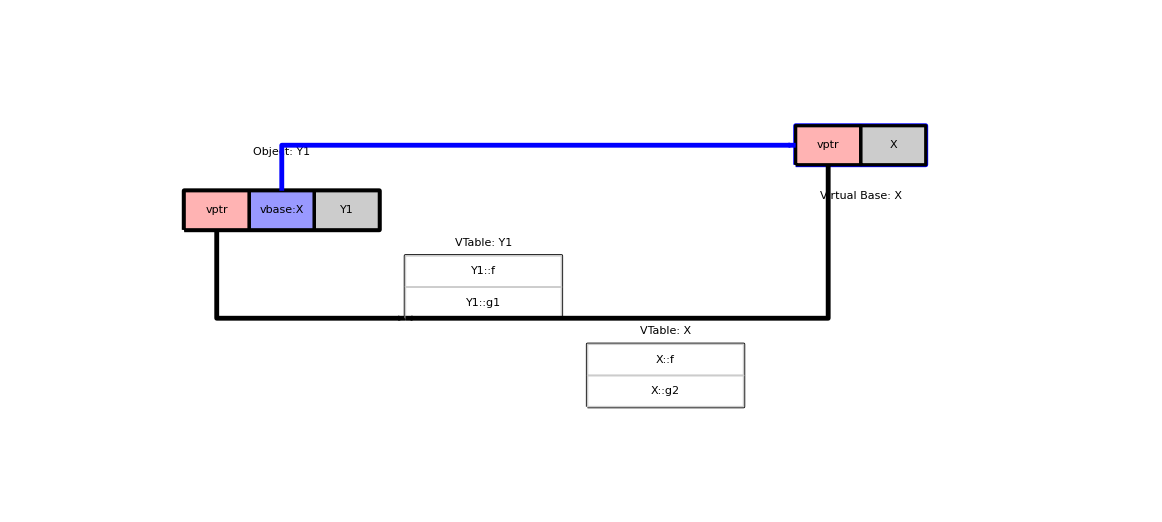

```mathematica
DrawClassDiagram[layoutY1]
```

```mathematica
layoutY2 = ComputeClassLayout[classes,"Y2"]
```

<|ClassName→Y2,Layout→{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,Align→8,ClassOfVtable→Y2,VTableEntries→{Y2::f,Y2::g2}|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,Align→8,IsVirtualBase→True,VBaseOf→X|>,<|Name→Y2,Kind→Class,Offset→16,Size→0,Align→1|>},VirtualBases→{<|ClassName→X,Layout→{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,Align→8,ClassOfVtable→Y2,VTableEntries→{X::f,X::g2}|>,<|Name→X,Kind→Class,Offset→8,Size→4,Align→4|>},TotalSize→16,MaxAlign→8,VTableEntries→{X::f,X::g2}|>},TotalSize→16,MaxAlign→8,VTableEntries→{Y2::f,Y2::g2}|>

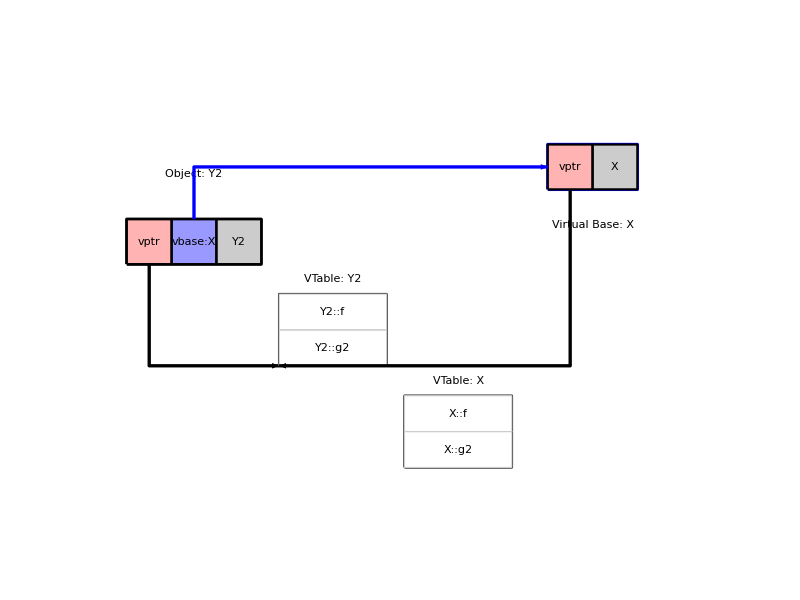

```mathematica
DrawClassDiagram[layoutY2]
```

```mathematica
layoutZ= ComputeClassLayout[classes,"Z"]
```

<|ClassName→Z,Layout→{<|Name→Y1,Kind→NonVirtualBase,Offset→0,Size→16,Align→8,Layout→{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,Align→8,ClassOfVtable→Z,VTableEntries→{Y1::f,Y1::g1}|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,Align→8,IsVirtualBase→True,VBaseOf→X|>,<|Name→Y1,Kind→Class,Offset→16,Size→0,Align→1|>}|>,<|Name→Y2,Kind→NonVirtualBase,Offset→16,Size→16,Align→8,Layout→{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,Align→8,ClassOfVtable→Z,VTableEntries→{Y2::f,Y2::g2}|>,<|Name→vbase:X,Kind→VbaseSlot,Offset→8,Size→8,Align→8,IsVirtualBase→True,VBaseOf→X|>,<|Name→Y2,Kind→Class,Offset→16,Size→0,Align→1|>}|>,<|Name→Z,Kind→Class,Offset→32,Size→0,Align→1|>},VirtualBases→{<|ClassName→X,Layout→{<|Name→vptr,Kind→Vptr,Offset→0,Size→8,Align→8,ClassOfVtable→Z,VTableEntries→{X::f,X::g2}|>,<|Name→X,Kind→Class,Offset→8,Size→4,Align→4|>},TotalSize→16,MaxAlign→8,VTableEntries→{X::f,X::g2}|>},TotalSize→32,MaxAlign→8,VTableEntries→{Z::f,Z::g1,Y2::g2}|>

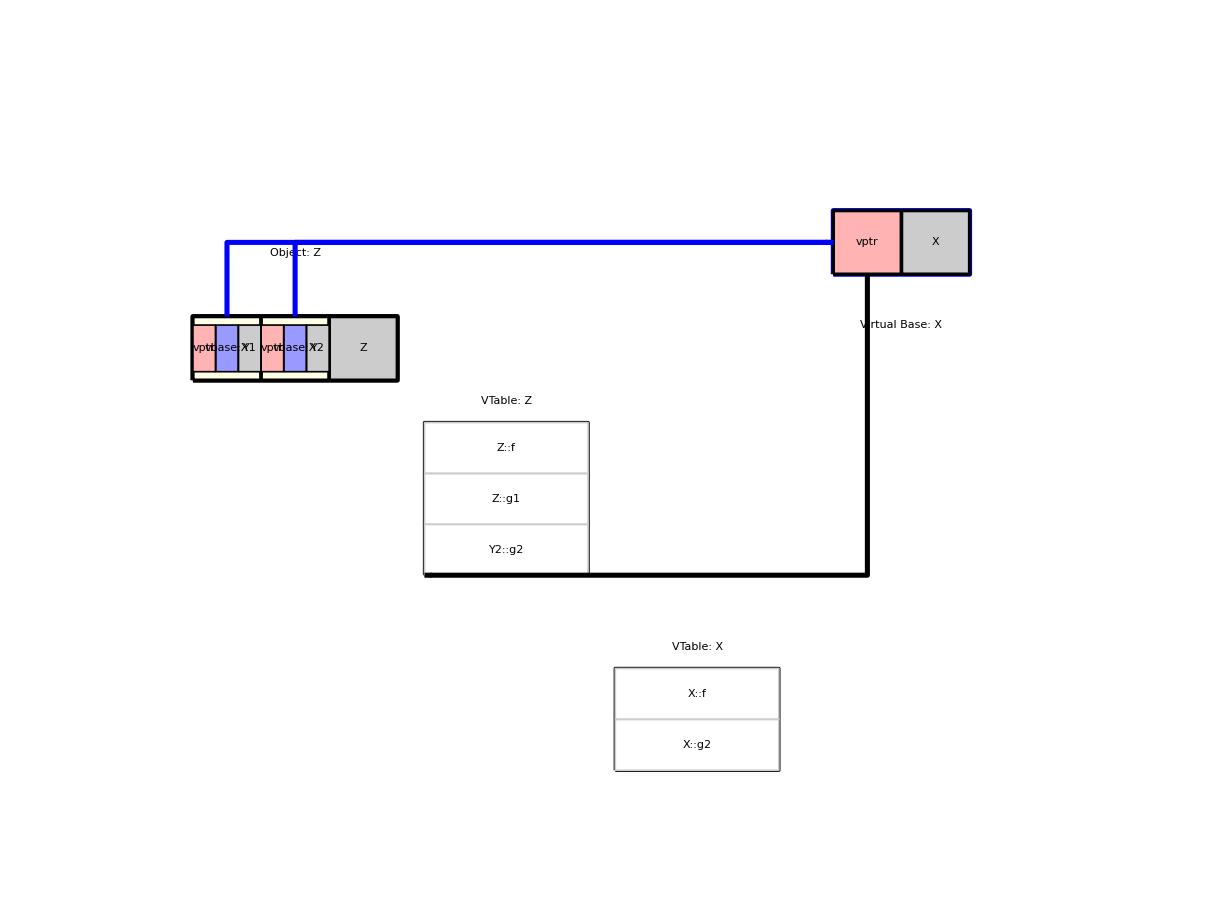

```mathematica
DrawClassDiagram[layoutZ]
```

```mathematica
classes=ParseCppToClasses["previos_exam_examples/Q2_W23-24_B.hpp"];
```

```mathematica
Quit[]
```